```mathematica
SetDirectory[NotebookDirectory[]];
datos=Import["datosTF.txt","Data"];
wpulsoz=datos[[2,1]];;  (*rad/fs*)(*Puslo láser*)
wpulsoz=wpulsoz/wpulsoz ; 
wpulsoy=2*wpulsoz; (*rad/fs*)(*Queremos generar el segundo armónico*)(*Ver luego el espectro generado con la TF*)
(*-----------------------------------Resonancia del medio dispersivo en z--------------------------*)
f1z=0.7; (*Hz/fs*)
delta1z=0.5*f1z; (*Hz/fs*) (*Constante de amortiguamiento*)
w1z=2*Pi*f1z/wpulsoz; (*rad/fs*) (*Frecuencia de Resonancia*)
εsz=2;
εinfz=1;
G1z=1;
b1z=G1z*(εsz-εinfz);
εrz[w_]:=εinfz+((εsz-εinfz)*w1z^2)/(w1z^2-2*I*w*delta1z-w^2);
n2z[w_]:=Abs[Sqrt[εrz[w]]]
"Índice de refracción wz"
n2z[wpulsoz]
(*-----------------------------------Resonancia del medio dispersivo en y--------------------------*)
f1y=0.5;
delta1y=0.2*f1y; (*Hz/fs*) (*Constante de amortiguamiento*)
w1y=2*Pi*f1y/wpulsoz; (*rad/fs*) (*Frecuencia de Resonancia*)
εinfy=1;
G1y=1;
b1y=G1y*(εsy-εinfy);
εry[w_,εsy_]:=εinfy+((εsy-εinfy)*w1y^2)/(w1y^2-2*I*w*delta1y-w^2);
n2y[w_,εsy_]:=Abs[Sqrt[εry[w,εsy]]]
calculo=NSolve[n2z[wpulsoz]-n2y[wpulsoy,εsy]==0,εsy]
sol=εsy/.calculo[[2]]
Abs[sol]
```

Índice de refracción wz

1.43296

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{εsy→-0.815887+0.123749 ⅈ},{εsy→1.62646-0.0426916 ⅈ}}

1.62646-0.0426916 ⅈ

1.62702

```mathematica
sol=εsy/.calculo[[2]]
(*sol=14.62702*)
n2y[wpulsoy,sol]

parterealey=Table[{w,Re[Sqrt[εry[w,sol]]]},{w,0,10,0.001}];
parterealez=Table[{w,Re[Sqrt[εrz[w]]]},{w,0,10,0.001}];
```

1.62646-0.0426916 ⅈ

1.43296

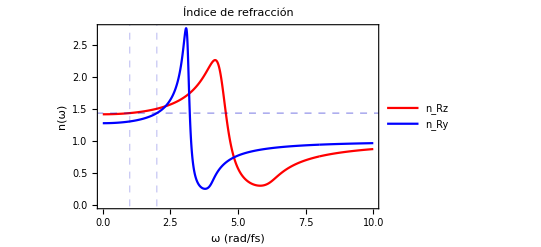

```mathematica
ListPlot[{parterealez,parterealey},PlotRange->All, Joined ->True,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}, Frame->True,FrameLabel->{"ω (rad/fs)","n(ω)"," "," "},PlotLabel->Style["Índice de refracción",16,Black],FrameStyle->{Black,Black,Black,Black},PlotLegends->Placed[{"n_Rz","n_Ry"},{Scaled[{0.8,0.8}], {0, 0.8}}],GridLines->{{{wpulsoy/wpulsoz,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{wpulsoz/wpulsoz,Directive[RGBColor[0,0,0.8],Dashed,Thick]}},{{n2z[wpulsoz],Directive[RGBColor[0,0,0.8],Dashed,Thick]},{n2y[wpulsoy,sol],Directive[RGBColor[0,0,0.8],Dashed,Thick]}}}]
```